# Alife 2022

## Part I: Generating an Example Circuit

#### Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
expA = "E2";
expB = "E2B";
```

```mathematica
dir2="E2B/45/";
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
fitness[e_,n_,t_]:=
Module[
{allevol,allfit,bestfit,bestindex,bestsorted},
allevol={};
allfit={};
bestfit  = {};
bestindex={};
For[i=0, i<n, i++,
evol = Transpose[Import[StringJoin[e,"/",ToString[i], "/fitness.dat"]]][[2]];
allevol=Append[allevol,evol];
fit=Last[evol];
allfit=Append[allfit,fit];
If[fit>t ,
bestfit = Append[bestfit,fit];
bestindex=Append[bestindex,i];
];
];
allevol = Sort[allevol,#1[[-1]]<#2[[-1]]&];
bestsorted = Sort[Transpose[{bestindex,bestfit}],#1[[2]]>#2[[2]]&];
{bestsorted,allevol,allfit}
]
```

## 1. Evolution

```mathematica
n=100;
t=0.5;
```

```mathematica
{bestsortedB,allevolB,allfitB} = fitness[expB,n,t];
Take[bestsortedB,{1,5}]
```

{{76,0.990228},{96,0.989447},{45,0.981455},{31,0.969797},{88,0.957066}}

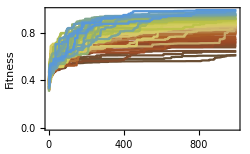
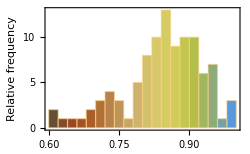
-Graphics-A
-Graphics-B

```mathematica
panelA = ListLinePlot[allevolB,Frame->True,PlotStyle->"SouthwestColors",FrameLabel->{"Generations","Fitness"},PlotRange->All,ImageSize->250];
panelB = Histogram[allfitB,20,PlotRange->All,ImageSize->250,Frame->True,ChartStyle->"SouthwestColors",FrameLabel->{"Final fitness","Relative frequency"}];
charts={panelA,panelB};
labels=CharacterRange["A","Z"][[;;2]];
panels=Partition[Panel[#,Style[#2,14],{{Left,Top}},Appearance->"Frameless",Background->White]&@@@Transpose[{charts,labels}],1];
Grid[panels,Alignment->{Left,Top}]
Export["Figure2.eps",%];
```

## 2. Generalization

```mathematica
ab={};
perf={};
For[i=0, i<n, i++,
a = Flatten[Import[StringJoin[expB,"/",ToString[i], "/A_finalperf.dat"]]][[1]];
b =Flatten[Import[StringJoin[expB,"/",ToString[i], "/B_finalperf.dat"]]][[1]];
ab = Append[ab,{a,b}];
perf = Append[perf,a b];
];
```

```mathematica
nPerf=(perf-Min[perf])/(Max[perf]-Min[perf]);
```

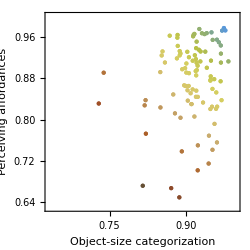

```mathematica
ListPlot[Partition[ab,1],PlotStyle->Table[{Directive[PointSize[Medium],ColorData["SouthwestColors"][nPerf[[x]]]]},{x,1,Length[perf]}],PlotRange->{{0.63,1},{0.63,1}},Frame->True,PlotStyle->Directive[PointSize[Medium],LightGray],AspectRatio->1,
FrameLabel->{"Object-size categorization","Perceiving affordances"},ImageSize->250]
Export["Figure3.eps",%];
```

```mathematica
perfindex = Transpose[{Table[x,{x,0,99}],perf}];
Take[Sort[perfindex,#1[[2]]>#2[[2]]&],{1,5}]
```

{{45,0.953616},{96,0.951823},{76,0.945107},{31,0.921556},{15,0.918328}}

## 3. Connectome

```mathematica
iw2 =Import[StringJoin[dir2, "/interweights.dat"]];
```

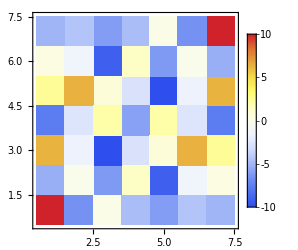

```mathematica
ListDensityPlot[iw2,PlotRange->{{0.5,7.5},{0.5,7.5},{-10,10}},PlotLegends->BarLegend[{Automatic,{-10,10}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["TemperatureMap"]]
```

## 4. Behavior

### Task 1: Object Recognition

```mathematica
ba=Import[ StringJoin[dir2,"B_avoid_aposx.dat"]];
bc=Import[ StringJoin[dir2,"B_approach_aposx.dat"]];
```

```mathematica
panelBb=Show[{ListLinePlot[ba,PlotStyle->cd[[1]]],
ListLinePlot[bc,PlotStyle->cd[[2]]]},PlotRange->{Automatic,{-45,45}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
```

-Graphics-

### Task 2: Perceiving Affordances

```mathematica
aa=Import[ StringJoin[dir2,"A_avoid_aposx.dat"]];
ac=Import[ StringJoin[dir2,"A_approach_aposx.dat"]];
```

```mathematica
panelAb=Show[{
ListLinePlot[ac,PlotStyle->cd[[4]]],
ListLinePlot[aa,PlotStyle->cd[[3]]]},
PlotRange->{Automatic,{-45,45}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
```

-Graphics-

## 5. Neural Activity

### ObjectSizeDisc

#### Avoid

```mathematica
ba1=Import[StringJoin[dir2,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir2,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir2,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir2,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir2,"B_avoid_n5.dat"]];
ba6=Import[StringJoin[dir2,"B_avoid_n6.dat"]];
ba7=Import[StringJoin[dir2,"B_avoid_n7.dat"]];
```

#### Approach

```mathematica
bc1=Import[StringJoin[dir2,"B_approach_n1.dat"]];
bc2=Import[StringJoin[dir2,"B_approach_n2.dat"]];
bc3=Import[StringJoin[dir2,"B_approach_n3.dat"]];
bc4=Import[StringJoin[dir2,"B_approach_n4.dat"]];
bc5=Import[StringJoin[dir2,"B_approach_n5.dat"]];
bc6=Import[StringJoin[dir2,"B_approach_n6.dat"]];
bc7=Import[StringJoin[dir2,"B_approach_n7.dat"]];
```

#### Viz

```mathematica
panelBn=GraphicsColumn[
{
Show[
{ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba6,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc6,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[ba7,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[bc7,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250]
}
]
```

-Graphics-

### Afford

#### Avoid

```mathematica
ba1=Import[StringJoin[dir2,"A_avoid_n1.dat"]];
ba2=Import[StringJoin[dir2,"A_avoid_n2.dat"]];
ba3=Import[StringJoin[dir2,"A_avoid_n3.dat"]];
ba4=Import[StringJoin[dir2,"A_avoid_n4.dat"]];
ba5=Import[StringJoin[dir2,"A_avoid_n5.dat"]];
ba6=Import[StringJoin[dir2,"A_avoid_n6.dat"]];
ba7=Import[StringJoin[dir2,"A_avoid_n7.dat"]];
```

#### Approach

```mathematica
bc1=Import[StringJoin[dir2,"A_approach_n1.dat"]];
bc2=Import[StringJoin[dir2,"A_approach_n2.dat"]];
bc3=Import[StringJoin[dir2,"A_approach_n3.dat"]];
bc4=Import[StringJoin[dir2,"A_approach_n4.dat"]];
bc5=Import[StringJoin[dir2,"A_approach_n5.dat"]];
bc6=Import[StringJoin[dir2,"A_approach_n6.dat"]];
bc7=Import[StringJoin[dir2,"A_approach_n7.dat"]];
```

#### Viz

```mathematica
panelAn=GraphicsColumn[
{
Show[
{ListLinePlot[bc1,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba1,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc2,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba2,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc3,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba3,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc4,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba4,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc5,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba5,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc6,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba6,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250],
Show[
{ListLinePlot[bc7,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}}],
ListLinePlot[ba7,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}}]}
,PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/8,ImageSize->250]
}
]
```

-Graphics-

## Combined figure of Behavior and Neural Activity per task

```mathematica
charts={panelBb,panelAb,panelBn,panelAn};
labels=CharacterRange["A","Z"][[;;4]];
panels=Partition[Panel[#,Style[#2,14],{{Left,Top}},Appearance->"Frameless",Background->White]&@@@Transpose[{charts,labels}],2];
Grid[panels,Alignment->{Left,Top}]
Export["Figure4.eps",%];
```

-Graphics-A | -Graphics-B
-Graphics-C | -Graphics-D

## Part II: Lesion - Functional Connectivity Analysis

## Two way Lesions

```mathematica
oneA =Import[StringJoin[dir2, "/oneway_sysedge_iw_A.dat"]];
oneB =Import[StringJoin[dir2, "/oneway_sysedge_iw_B.dat"]];
```

```mathematica
ListDensityPlot[oneA,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["SunsetColors"]]
ListDensityPlot[oneB,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["SunsetColors"]]
```

-Graphics-

-Graphics-

## One way Lesions

```mathematica
twoA =Import[StringJoin[dir2, "/sysedge_iw_A.dat"]];
twoB =Import[StringJoin[dir2, "/sysedge_iw_B.dat"]];
```

```mathematica
ListDensityPlot[twoA,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["SunsetColors"]]
ListDensityPlot[twoB,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["SunsetColors"]]
```

-Graphics-

-Graphics-

## FC using Pearson' s Correlation

```mathematica
fcPCA =Import[StringJoin[dir2, "/fc_corr_A_both.dat"]];
fcPCB =Import[StringJoin[dir2, "/fc_corr_B_both.dat"]];
```

```mathematica
ListDensityPlot[fcPCA,PlotRange->{{-0.5,6.5},{-0.5,6.5},{-1,1}},PlotLegends->BarLegend[{Automatic,{-1,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["TemperatureMap"]]
ListDensityPlot[fcPCB,PlotRange->{{-0.5,6.5},{-0.5,6.5},{-1,1}},PlotLegends->BarLegend[{Automatic,{-1,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["TemperatureMap"]]
```

-Graphics-

-Graphics-

## FC using Mutual Information

```mathematica
fcMIA =Import[StringJoin[dir2, "/fc_mi_A_both.dat"]];
fcMIB =Import[StringJoin[dir2, "/fc_mi_B_both.dat"]];
```

```mathematica
ListDensityPlot[fcMIA,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["BlueGreenYellow"]]
ListDensityPlot[fcMIB,PlotRange->{{-0.5,6.5},{-0.5,6.5},{0,1}},PlotLegends->BarLegend[{Automatic,{0,1}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["BlueGreenYellow"]]
```

-Graphics-

-Graphics-

## FC using Transfer Entropy

```mathematica
fcTEA =Import[StringJoin[dir2, "/fc_te_A_both.dat"]];
fcTEB =Import[StringJoin[dir2, "/fc_te_B_both.dat"]];
```

```mathematica
min = Min[{Min[Transpose[fcTEA][[3]]],Min[Transpose[fcTEB][[3]]]}]
max = Max[{Max[Transpose[fcTEA][[3]]],Max[Transpose[fcTEB][[3]]]}]
```

0.

1.00604275818786348

```mathematica
ListDensityPlot[fcTEA,PlotRange->{{-0.5,6.5},{-0.5,6.5},{min,max}},PlotLegends->BarLegend[{Automatic,{min,max}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["StarryNightColors"]]
ListDensityPlot[fcTEB,PlotRange->{{-0.5,6.5},{-0.5,6.5},{min,max}},PlotLegends->BarLegend[{Automatic,{min,max}}],InterpolationOrder->0,ColorFunctionScaling->True,ImageSize->250,ClippingStyle->Automatic,ColorFunction->ColorData["StarryNightColors"]]
```

-Graphics-

-Graphics-

## Comparison between Two-Way Lesions and FC PC

```mathematica
Show[
{
Graphics[{LightGray,Table[Line[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}][[x]],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}][[x]]}],{x,1,Length[oneA]}]}],
ListPlot[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}]},PlotRange->All,PlotStyle->PointSize[Medium]]
},
AspectRatio->1,Frame->True,FrameLabel->{"Pearson's Correlation","Two-way information lesions"},ImageSize->250
]
```

-Graphics-

## Comparison between Two-Way Lesions and FC PC

```mathematica
Show[
{
Graphics[{LightGray,Table[Line[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}][[x]],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}][[x]]}],{x,1,Length[oneA]}]}],
ListPlot[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}]},PlotRange->All,PlotStyle->PointSize[Medium]]
},
AspectRatio->1,Frame->True,FrameLabel->{"Mutual Information","Two-way information lesions"},ImageSize->250
]
```

-Graphics-

## Comparison between One-Way Lesions and FC TE

```mathematica
Show[
{
Graphics[{LightGray,Table[Line[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}][[x]],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}][[x]]}],{x,1,Length[oneA]}]}],
ListPlot[{Transpose[{Transpose[fcTEA][[3]],Transpose[oneA][[3]]}],Transpose[{Transpose[fcTEB][[3]],Transpose[oneB][[3]]}]},PlotRange->All,PlotStyle->PointSize[Medium]]
},
AspectRatio->1,Frame->True,FrameLabel->{"Transfer Entropy","One-way information lesions"},ImageSize->250
]
```

-Graphics-